# κτS^2

# Secondary structure (S^2)assignment to residues of proteins based on the curvature (κ) and torsion (τ) of the backbone.

## Curvature-torsion pairs

## Read a list of PDB codes from the PDB repository and cure data to obtain: (i) the coordinates of the backbone atoms (of chain A) of the PDB, and (ii) the author’s secondary structure labeling. In the following notebook, as a user, you must follow a few steps in order to assign a secondary structure of a specific protein. Sections highlighter with yellow are key for changing a PDB code of a protein of interest or to visualize the results.

### Reading the necessary information from the PDB repository

PDB code

list[pdb] is the list of  PDB codes of the proteins. The set of proteins can be increased by adding new PDB codes at the end of this list.

```mathematica
list[pdb]={"1UBQ"};
```

Importing lines

Generate the importing lines for each protein

```mathematica
list[import]=Table[StringJoin["https://files.rcsb.org/download/",list[pdb]⟦i⟧,".pdb"],{i,Length[list[pdb]]}];
```

List of  import lines to obtain the data (residue atoms) from the PDB files.

```mathematica
list[atoms]=Table[Import[list[import]⟦i⟧,{"PDB","ResidueAtoms"}],{i,1,Length[list[import]]}];
```

List of import lines for the residue coordinates. The residue coordinates are divided by 100 - This due to the use of different units in the PDB generated by Wolfram

```mathematica
Length[Flatten[list[coordinates]]];
```

```mathematica
list[coordinates]=Table[Import[list[import]⟦i⟧,{"PDB","ResidueCoordinates"}]/100.,{i,1,Length[list[import]]}];
```

List  of import lines for the author’s secondary structure

```mathematica
list[ss,0]=Table[Import[list[import]⟦i⟧,{"PDB","SecondaryStructure"}],{i,1,Length[list[import]]}];
```

### Processing the information from PDB

The function range[{x,y}] produces integer numbers in the range {x,y}.

```mathematica
range[{x_,y_}]:=Range[x,y]
```

#### Backbone

coordinate assignment to the atoms of the backbone.
there are multiple chains, Only the chain labeled “A” is taken

```mathematica
list[backbone,0]=Table[Thread[list[atoms]⟦i,1,;;⟧->list[coordinates]⟦i,1,;;⟧],{i,Length[list[atoms]]}];
```

```mathematica
list[backbone,1]=Table[Thread[list[backbone,0]⟦i,j⟧],{i,Length[list[backbone,0]]},{j,1,Length[list[backbone,0]⟦i⟧]}];
```

```mathematica
Length[Flatten[list[backbone,3]]];
```

Delete cases with residues shorter than 3 atoms.

```mathematica
list[backbone,2]=Table[DeleteCases[list[backbone,1]⟦i⟧,z_/;Length[z]<3],{i,Length[list[backbone,1]]}];
```

Delete cases with HETATOMS

```mathematica
list[backbone,3]=Table[DeleteCases[list[backbone,2]⟦i⟧,z_/;z⟦1,1⟧≠ "N"||z⟦2,1⟧≠ "C"||z⟦3,1⟧≠ "C"],{i,Length[list[backbone,2]]}];
```

Select only the backbone of the protein, atoms 1 to 3 of each residue.

```mathematica
Length[Flatten[list[backbone]]]
```

3150

```mathematica
list[backbone]=list[backbone,3]⟦;;,;;,1;;3,2⟧;
```

The array list[backbone] is described by 4 indices: the first index is the protein index, the second index is the residue index, the third index (with values 1 to 3) is the atom of the residue (N, C_α, CO), and the forth index is the (x,y,z) coordinate of each atom of the residues.

The generalized bonds sequence for each protein (warnings are due to mismatch between some of the arrays obtained from the PDB file, this troublesome proteins will be dropped below)

```mathematica
list[backbone,atoms]=Table[Flatten[list[backbone]⟦i⟧,{1,2}],{i,Length[list[backbone]]}];
```

#### Secondary structure

Secondary structure of chain A
It is necessary (to facilitate the data curation) to add a  {0,0} in the gaps ({}).

```mathematica
list[ss,1]=list[ss,0]/.{}->{{0,0}};
```

Lists of residues which are labeled alpha Helices

```mathematica
list[helix,1]=list[ss,1]⟦;;,1,2,1⟧;
```

List of residues which are labeled beta Sheet

```mathematica
list[sheet,1]=list[ss,1]⟦;;,2,2,1⟧;
```

List of residues which are labeled alpha helix, beta sheet or (by complement) a gamma-coil

```mathematica
list[helix]=Table[Flatten[Table[range[list[helix,1]⟦j,i⟧],{i,Length[list[helix,1]⟦j⟧]}]],{j,Length[list[helix,1]]}];
list[sheet]=Table[Flatten[Table[range[list[sheet,1]⟦j,i⟧],{i,Length[list[sheet,1]⟦j⟧]}]],{j,Length[list[sheet,1]]}];
list[coil]=Table[Complement[Range[Length[list[backbone]⟦i⟧]],Flatten[{list[helix]⟦i⟧,list[sheet]⟦i⟧}]],{i,Length[list[backbone]]}];
```

### Filtering mistaken data

Eliminate proteins that involved no-amino proteins

```mathematica
list[elimination]=Position[list[backbone],{}];
```

Eliminate the wrong data

```mathematica
Flatten[list[backbone,atoms]];
```

```mathematica
Length[Flatten[list[backbone,atoms]]];
```

```mathematica
list[helix]=Delete[list[helix],list[elimination]];
list[sheet]=Delete[list[sheet],list[elimination]];
list[coil]=Delete[list[coil],list[elimination]];
list[backbone]=Delete[list[backbone],list[elimination]];
list[backbone,atoms]=Delete[list[backbone,atoms],list[elimination]];
```

### Export the relevant data

```mathematica
Export[ToString[NotebookDirectory[]<>"backbones_prot_186.dat"],list[backbone],"Table"];
Export[ToString[NotebookDirectory[]<>"helices_prot_186.dat"],list[helix],"Table"];
Export[ToString[NotebookDirectory[]<>"sheets_prot_186.dat"],list[sheet],"Table"];
Export[ToString[NotebookDirectory[]<>"coils_prot_186.dat"],list[coil],"Table"];
```

## Generate the list of curvature and torsion for each residue

### Generate the arrays 𝒜 (atoms), ℬ (bonds), 𝒩 (normals to neighbor bonds), 𝒴 (y axis to each bond)

The general arrays, 𝒜 is the backbone’s  atoms coordinates, ℬ is the bond vectors for the backbone, 𝒩 is the normal vector to three bond atoms on the backbone, 𝒴 is the y axis to each bond

𝒜[i], i∈{1, ...., 3N}

ℬ[i], with i∈{1, ..., 3N-1}, i=1 is for N atom of the 1st residue, i=3N-1 is for the Cα of the N-th residue 

𝒩[i] and 𝒵[i], with i∈{1, ..., 3N-2}, i=1 is for Cα of the 1st residue, i=3N-2 is for the Cα of the N-th residue 

𝒳[i] and 𝒴[i], with i∈{1, ..., 3N-2}, i=1 is for Cα of the 1st  residue, i=3N-2 is for the Cα of the N-th residue

index alignment: 𝒜[i+1] : ℬ[i+1] : 𝒳[i] : 𝒵[i] : 𝒴[i]

```mathematica
𝒜=list[backbone,atoms];
ℬ=Table[𝒜⟦i,j+1⟧-𝒜⟦i,j⟧,{i,Length[𝒜]},{j,1,Length[𝒜⟦i⟧]-1}];
𝒩=Table[Cross[ℬ⟦i,j⟧,-ℬ⟦i,j-1⟧],{i,Length[ℬ]},{j,2,Length[ℬ⟦i⟧]}];

𝒳=Table[Normalize[ℬ⟦i,j⟧],{i,Length[ℬ]},{j,2,Length[ℬ⟦i⟧]}];
𝒵=Table[Normalize[𝒩⟦i,j⟧],{i,Length[𝒩]},{j,1,Length[𝒩⟦i⟧]}];
𝒴=Table[Cross[𝒵⟦i,j⟧,𝒳⟦i,j⟧],{i,Length[𝒵]},{j,1,Length[𝒵⟦i⟧]}];
```

### Obtain the curvature κ

The center 𝒸[i] of the circle that crosses three atoms 𝒜[i-1], 𝒜[i], and 𝒜[i+1] is given by the the equations
𝒸·𝒸==(ℬ[i-1]-𝒸)·(ℬ[i-1]-𝒸),  𝒸·𝒸==(ℬ[i]-𝒸)·(ℬ[i]-𝒸), and 𝒸·(ℬ[i]×B[i-1])==0. The last equation can be written as: c·𝒩[i]=0

𝒞 is an auxiliary vector to obtain the ratio of curvature. 
𝒞[i], with i={1,3N-2},  i=1 is for Cα of the 1st  residue, i=3N-2 is for the Cα of the N-th residue.

```mathematica
𝒞=Table[{(ℬ⟦i,j-1⟧.ℬ⟦i,j-1⟧)/2,-(ℬ⟦i,j⟧.ℬ⟦i,j⟧)/2,0},{i,Length[ℬ]},{j,2,Length[ℬ⟦i⟧]}];
```

𝒞L is an auxiliary matrix used in the calculation of the ratio of curvature.
𝒞L[i], with i={1,3N-2},  i=1 is for Cα of the 1st  residue, i=3N-2 is for the Cα of the N-th residue

```mathematica
𝒞L=Table[Inverse[{ℬ⟦i,j-1⟧,ℬ⟦i,j⟧,𝒩⟦i,j-1⟧}],{i,Length[ℬ]},{j,2,Length[𝒩⟦i⟧]+1}];
```

The curvature κ.
κ[i], with i={1,3N-2},  i=1 is for Cα of the 1st  residue, i=3N-2 is for the Cα of the N-th residue

```mathematica
κ=Table[1/Norm[𝒞L⟦i,j⟧.𝒞⟦i,j⟧],{i,Length[𝒞]},{j,Length[𝒞L⟦i⟧]}];
```

### Calculate the 1-4 torsion

Calculate the generalized torsion vector from the generalized vectors 𝒵 and 𝒴.

𝒯[i], with i={1,3N-3},  i=1 is for Cα of the 1st  residue, i=3N-3 is for the N atom of the N-th residue

```mathematica
𝒯=Table[ArcTan[𝒵⟦i,j+1⟧.𝒵⟦i,j⟧,𝒵⟦i,j+1⟧.𝒴⟦i,j⟧],{i,Length[𝒵]},{j,Length[𝒵⟦i⟧]-1}];
```

### Calculate the 1-5 torsion

Calculate the generalized 1-5 torsion vector from the generalized vectors 𝒵 and 𝒴.
𝒟[i], with i={1,3N-4},  i=1 is for Cα of the 1st  residue, i=3N-3 is for the N atom of the N-th residue

```mathematica
(*𝒟=Table[ArcCos[(𝒩⟦i,j⟧.𝒩⟦i,j+2⟧)/(Norm[𝒩⟦i,j⟧]Norm[𝒩⟦i,j+2⟧])],{i,1,Length[𝒩]},{j,1,Length[𝒩⟦i⟧]-2}];*)
```

```mathematica
𝒟=Table[ArcTan[𝒵⟦i,j+2⟧.𝒵⟦i,j⟧,𝒵⟦i,j+2⟧.𝒴⟦i,j⟧],{i,1,Length[𝒵]},{j,1,Length[𝒵⟦i⟧]-2}];
```

### Ramachandran angles

Ramachandran angles ω, ϕ, ψ

```mathematica
ψ=-𝒯⟦;;,1;;;;3⟧;
ω=-𝒯⟦;;,2;;;;3⟧;
ϕ=-𝒯⟦;;,3;;;;3⟧;
```

### Pairing Curvature and Ramachandran angles

Ramachandran angles ϕψ pairing

```mathematica
ϕψ=Table[Transpose[{ϕ⟦i⟧,ψ⟦i⟧}],{i,Length[ϕ]}];
```

```mathematica
Ramachandran=ListPlot[ϕψ,AxesLabel->{"ϕ","ψ"}];
```

The angle ψ can be associated to the curvature on the Cα carbon and on the CO carbon

```mathematica
κψCα=Table[Transpose[{Delete[κ⟦i,1;;;;3⟧,-1],ψ⟦i⟧}],{i,Length[κ]}];
κψCO=Table[Transpose[{κ⟦i,2;;;;3⟧,ψ⟦i⟧}],{i,Length[κ]}];
```

The angle ω can be associated to the curvature on the CO carbon and on the N atom of next residue

```mathematica
κωCO=Table[Transpose[{κ⟦i,2;;;;3⟧,ω⟦i⟧}],{i,Length[κ]}];
κωN=Table[Transpose[{κ⟦i,3;;;;3⟧,ω⟦i⟧}],{i,Length[κ]}];
```

The angle ϕ can be associated to the curvature on the N atom and α carbon

```mathematica
κϕN=Table[Transpose[{κ⟦i,3;;;;3⟧,ϕ⟦i⟧}],{i,Length[κ]}];
κϕCα=Table[Transpose[{κ⟦i,4;;;;3⟧,ϕ⟦i⟧}],{i,Length[κ]}];
```

κτS^2 pairs

The pair using 1-5 torsions

```mathematica
κδ1=Table[Transpose[{Delete[κ⟦i,2;;⟧,-1],𝒟⟦i⟧}],{i,Length[κ]}];
κδ=Table[Prepend[Append[κδ1⟦i⟧,Last[κδ1⟦i⟧]],First[κδ1⟦i⟧]],{i,Length[κ]}];
κδN=κδ⟦;;,1;;;;3⟧;
κδCα1=κδ⟦;;,2;;;;3⟧;
κδCα=Table[Append[κδCα1⟦i⟧,Last[κδCα1⟦i⟧]],{i,Length[κδCα1]}];
```

Ramachandran plot

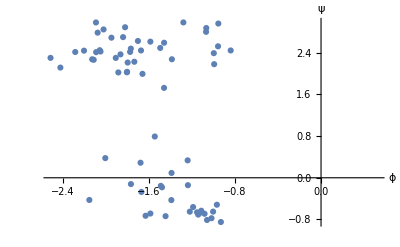

```mathematica
Ramachandran
```

# Secondary Structure Assignment

## Initialization of the program

### Data

```mathematica
αβγscoring=Import[ToString[NotebookDirectory[]<>"probability_hsc_prot_186.dat"],"Table"];
```

```mathematica
dataα=Table[{αβγscoring⟦i,1;;2⟧,αβγscoring⟦i,3⟧},{i,Length[αβγscoring]}];
dataβ=Table[{αβγscoring⟦i,1;;2⟧,αβγscoring⟦i,4⟧},{i,Length[αβγscoring]}];
dataγ=Table[{αβγscoring⟦i,1;;2⟧,αβγscoring⟦i,5⟧},{i,Length[αβγscoring]}];
```

```mathematica
functionα=Interpolation[dataα];
functionβ=Interpolation[dataβ];
functionγ=Interpolation[dataγ];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
range1={{x,0.51,0.9899999999999978},{y,-3.041592653589793,3.158407346410199}};
```

### Visualization of Secondary Structure Element of a random selected protein in the KvsT space (Data)

SSRegion represents the region plot for each secondary structure element in the κ vs τ space of 182 proteins.

```mathematica
SSRegion=Show[RegionPlot[functionα[x,y]≥ 0.5,range1⟦1⟧,range1⟦2⟧, PlotStyle->{Opacity[0.2],Red},BoundaryStyle->Red,PlotPoints->60],
RegionPlot[functionβ[x,y]>0.45,range1⟦1⟧,range1⟦2⟧,PlotStyle->{Opacity[0.2],Green},BoundaryStyle->Green,PlotPoints->60],
RegionPlot[functionγ[x,y]>0.476,range1⟦1⟧,range1⟦2⟧,PlotStyle->{Opacity[0.2],Blue},BoundaryStyle->Blue,PlotPoints->60],RegionPlot[0.0<Max[{Abs[functionα[x,y]-functionβ[x,y]],Abs[functionα[x,y]-functionγ[x,y]],Abs[functionγ[x,y]-functionβ[x,y]]}]<0.333,range1⟦1⟧,range1⟦2⟧,PlotStyle->{Opacity[0.2],Gray},BoundaryStyle->Gray,PlotPoints->60]];
```

```mathematica
Region1=ImplicitRegion[functionα[x,y]≥ 0.5,{x,y}];
Region2=ImplicitRegion[functionβ[x,y]>0.45,{x,y}];
Region3=ImplicitRegion[functionγ[x,y]>0.476,{x,y}];
```

```mathematica
RegionPlot[Region1,PlotRange->{range1⟦1,2;;3⟧,range1⟦2,2;;3⟧}];
RegionPlot[Region2,PlotRange->{range1⟦1,2;;3⟧,range1⟦2,2;;3⟧}];
RegionPlot[Region3,PlotRange->{range1⟦1,2;;3⟧,range1⟦2,2;;3⟧}];
```

```mathematica
regionID=Transpose[{Table[RegionMember[Region1,κδCα⟦1,i⟧],{i,Length[κδCα⟦1⟧]}],Table[RegionMember[Region2,κδCα⟦1,i⟧],{i,Length[κδCα⟦1⟧]}],Table[RegionMember[Region3,κδCα⟦1,i⟧],{i,Length[κδCα⟦1⟧]}]}]/.{True->1,False->0};
```

```mathematica
colorF[x_,y_,z_]:=RGBColor[x,y,z]
```

```mathematica
colours=Table[colorF[regionID⟦i,1⟧,regionID⟦i,2⟧,regionID⟦i,3⟧],{i,Length[regionID]}]
```

{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 1],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 1, 1],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 1, 0]}

### Protein accuracy for Secondary Structure Elements

#### Protein SS information

```mathematica
κδCα⟦1⟧;
Length[κδCα⟦1⟧]
```

76

```mathematica
helicesresidues=list[helix]⟦1⟧
sheetsresidues=list[sheet]⟦1⟧
coilsresidues=list[coil]⟦1⟧
```

{23,24,25,26,27,28,29,30,31,32,33,34,56,57,58,59}

{1,2,3,4,5,6,7,10,11,12,13,14,15,16,17,40,41,42,43,44,45,48,49,50,64,65,66,67,68,69,70,71,72}

{8,9,18,19,20,21,22,35,36,37,38,39,46,47,51,52,53,54,55,60,61,62,63,73,74,75,76}

```mathematica
αhelicesvalues=κδCα⟦1⟧⟦list[helix]⟦1⟧⟧;
βsheetsvalues=κδCα⟦1⟧⟦list[sheet]⟦1⟧⟧;
γcoilsvalues=κδCα⟦1⟧⟦list[coil]⟦1⟧⟧;
```

#### Region visualization and Statistics for SS

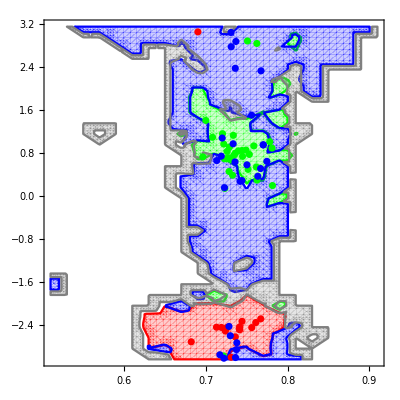

```mathematica
ssrprotein=Show[SSRegion,ListPlot[αhelicesvalues,PlotRange->All,PlotStyle->Red],ListPlot[βsheetsvalues,PlotRange->All,PlotStyle->Green],ListPlot[γcoilsvalues,PlotRange->All,PlotStyle->Blue],PlotRange->All]
```

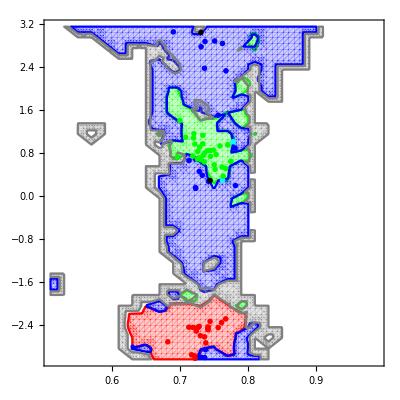

```mathematica
Show[SSRegion,Graphics[Table[{colours⟦i⟧,PointSize[0.01],Point[κδCα⟦1,i⟧]},{i,Length[κδCα⟦1⟧]}],PlotRange->{range1⟦1,2;;3⟧,range1⟦2,2;;3⟧}]]
```

```mathematica
grid0=Table[0,{i,Length[κδCα⟦1⟧]}];
helicesabs=Total@Table[ReplacePart[grid0,1,helicesresidues⟦i⟧],{i,Length[helicesresidues]}];
sheetsabs=Total@Table[ReplacePart[grid0,1,sheetsresidues⟦i⟧],{i,Length[sheetsresidues]}];
coilsabs=Total@Table[ReplacePart[grid0,1,coilsresidues⟦i⟧],{i,Length[coilsresidues]}];
probabilitieshelices=Table[functionα[κδCα⟦1,ni,1⟧,κδCα⟦1,ni,2⟧],{ni,Length[κδCα⟦1⟧]}];
probabilitiessheets=Table[functionβ[κδCα⟦1,ni,1⟧,κδCα⟦1,ni,2⟧],{ni,Length[κδCα⟦1⟧]}];
probabilitiescoils=Table[functionγ[κδCα⟦1,ni,1⟧,κδCα⟦1,ni,2⟧],{ni,Length[κδCα⟦1⟧]}];
allQH=Abs[probabilitieshelices-helicesabs];
allQE=Abs[probabilitiessheets-sheetsabs];
allQC=Abs[probabilitiescoils-coilsabs];
```

```mathematica
valueQH=Mean[1-allQH]
```

0.84072

```mathematica
valueQE=Mean[1-allQE]
```

0.665201

```mathematica
valueQC=Mean[1-allQC]
```

0.58352

```mathematica
σQH=StandardDeviation[probabilitieshelices]
```

0.347402

```mathematica
σQE=StandardDeviation[probabilitiessheets]
```

0.281182

```mathematica
σQC=StandardDeviation[probabilitiescoils]
```

0.217099